## Haagerup chain data analysis

### I/O

```mathematica
Labels[type_] := SortBy[StringDrop[StringSplit[#,"/"][[-1]],Switch[type,"m",-2,_,-3]]&/@FileNames[NotebookDirectory[]<>"/"<>type<>"/*."<>type],{Cutoff[#],U[#],J[#],NSites[#]}&];
Job[label_] := StringSplit[label,"_"][[1]];
BC[label_] := StringSplit[label,"_"][[2]];
NSites[label_] := ToExpression[StringSplit[label,"_"][[3]]];
MaxDim[label_] := ToExpression[StringSplit[label,"_"][[4]]];
Cutoff[label_] := StringSplit[label,"_"][[5]];
Prec[label_] := StringSplit[label,"_"][[6]];
J[label_] := StringSplit[label,"_"][[7]];
U[label_] := ToExpression[StringSplit[label,"_"][[8]]];
Charge[label_] := ToExpression[StringSplit[label,"_"][[9]]];
ReadData[label_,type_] := Module[{stream, str},
stream = OpenRead[NotebookDirectory[]<>"/"<>type<>"/"<>label<>"."<>type];
str = ReadString[stream];
Close[stream];
str = StringReplace[str,"e"->"*10^"];
If[type!="m"&&type≠"an",
str = "{" <> StringDrop[StringReplace[StringReplace[str,"\n"->""],",}"->"}"],-1]<> "}"//ToExpression
];
str//ToExpression
];
SetOptions[ListPlot,{BaseStyle->{FontSize->13}, PlotMarkers->{None,Tiny}}];
```

### Central charge from entanglement entropy

```mathematica
AnalyzeEE[name_] := Module[{len,Y,X,L,ansatz,fit,model,c,A,x},
Y = ReadData[name,"ee"] ;
len = Length[Y];
X = Y[[-1]];
L = NSites[name];
X = Select[X, L/5<#[[1]]<L*4/5&&OddQ[#[[1]]]&];
ansatz = c/If[BC[name]=="o",6,3] Log[L/π Sin[π x/L]]+A;
fit = FindFit[X,ansatz,{c,A},x];
model = ansatz/.fit;Show[ListPlot[#&/@Y,AxesLabel->{"l","S_l"},PlotLabel->"c = " <> ToString[SetPrecision[c/.fit,3]]<>"  :  J = " <> ToString[J[name]] <> "  L = " <> ToString[NSites[name]],PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}])],
Plot[{model},{x,0,L}]]
];
```

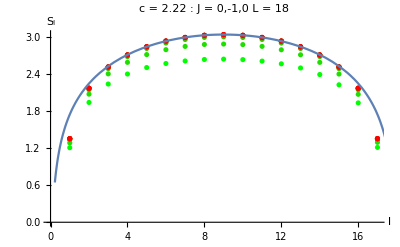

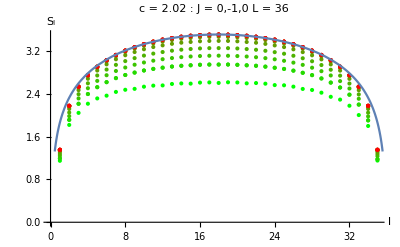

```mathematica
period = 3;
j = "0,-1,0";
plots = AnalyzeEE[#]&/@Select[Labels["ee"],Job[#]== "haagerupq"&&BC[#]=="p"&&Cutoff[#]=="1e-08"&&J[#]==j&&U[#]==2&&Charge[#]==0&&IntegerQ[NSites[#]/period]&&IntegerQ[NSites[#]/18]&];
Print[#]&/@plots;
```

### Scaling dimension from energy

```mathematica
ansatz = α L+β+γ/L+δ/L^2;
fitGSEnergy[gsEnergies_,show_] := Module[{fit,GSEnergy,Energy},
fit = FindFit[{#[[1]],#[[2]]}&/@gsEnergies,ansatz/L,{α,β,γ,δ},L];
If[show,
Print[Show[
ListPlot[gsEnergies,Joined->False,PlotLabel->ToString[InputForm[ansatz]]<>"\n{α,β,γ,δ} = "<>ToString[SetAccuracy[{α,β,γ,δ}/.fit,4]],AxesLabel->{"N","E_0"},PlotRange->{{0,36},{-.9,Automatic}}],
Plot[ansatz/L/.fit,{L,0,36}]
]]
];
GSEnergy[L0_] := ansatz/.fit/.{L->L0};
Energy[L0_,E0_] := (E0-GSEnergy[L0])/(-γ/.fit)*L0/12;
Energy
];

EnergyPlot[Energy_,spectra_] := ListPlot[Table[Energy[s[[1]],#[[1]]]&/@s[[2]],{s,spectra}],PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[Length[spectra]-1,1]),{k,1,Length[spectra]}])]
```

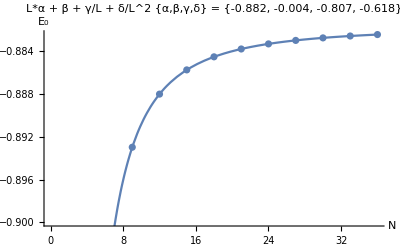

```mathematica
period = 3;
ζ = (3+Sqrt[13])/2;
j = "-1,-1,0";
q = 0;
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],J[#]==j&&Charge[#]===0&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
gsEnergies = {#[[1]],#[[2,1,1]]/#[[1]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],J[#]==j&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
Energy = fitGSEnergy[gsEnergies,True];
```

### Spectral analysis

```mathematica
tol = 5*10^-2;
CollectByRho[Energy_,spectrum_] := Module[{L = spectrum[[1]]},
Join[
Table[{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],Length[#]==3&&Abs[#[[3]]-r]/Abs[r]<tol&],{r,{ζ,-1/ζ}}],
{{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],Length[#]==2||Abs[#[[3]]-ζ]/ζ>tol&&Abs[#[[3]]+1/ζ]*ζ>tol&]}
]
];

styles = {Black,Black,Red};
markers = {"●","○","●"};
height = 2;
Spectrum[Energy_,spectrum_,c_,plotLabel_] := Module[{L=spectrum[[1]],spectrumByRho = CollectByRho[Energy,spectrum],plots},
plots = Table[ListPlot[{#[[1]],#[[2]]*c}&/@spectrumByRho[[i]],PlotMarkers->{markers[[i]],9},PlotStyle->styles[[i]]],{i,1,3}];
If[Mod[L,3]==0,
AppendTo[plots, Plot[{1,2},{x,-100,100},PlotStyle->{{Black,Dashed,Thin}}]];
];
If[Mod[L,3]≠0,
AppendTo[plots, Plot[{1/3,2/3},{x,-100,100},PlotStyle->{{Black,Dashed,Thin}}]];
];
Do[AppendTo[plots,ParametricPlot[{i,y},{y,0,height},PlotStyle->{{Black,Dashed,Thin}}]],{i,-Floor[L/2],L/2}];
Show[plots,PlotLabel->plotLabel,AxesOrigin->{0,0},PlotRange->{{-L/2,L/2},{0,height}},AxesLabel->{"p","Δ"},ImageSize->{Automatic,200},AspectRatio->height/L]
];

SpectrumIncludingFit[L0_,j_,q_] := Module[{},
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],J[#]==j&&Charge[#]===0&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
gsEnergies = {#[[1]],#[[2,1,1]]/#[[1]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],J[#]==j&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
Energy = fitGSEnergy[gsEnergies,False];
Spectrum[Energy,Spec[L0],2,"c=2  J="<>j<>"  L="<>ToString[L0]]
]
```

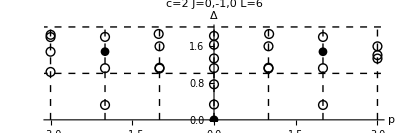

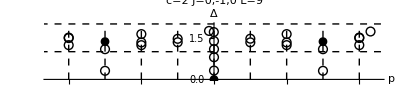

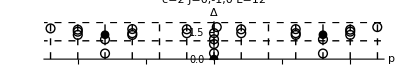

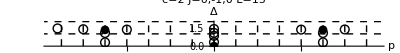

```mathematica
plots = Table[SpectrumIncludingFit[L0,j,q],{L0,6,15,3},{j,{"0,-1,0"}},{q,0,0}]//Flatten;
Print[#]&/@plots;
```

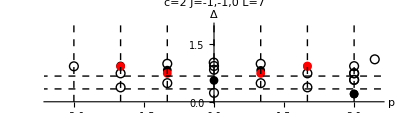

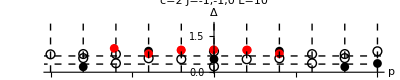

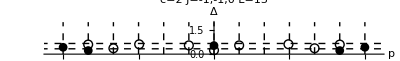

```mathematica
plots = Table[SpectrumIncludingFit[L0,j,q],{L0,7,13,3},{j,{"-1,-1,0"}},{q,0,0}]//Flatten;
Print[#]&/@plots;
```

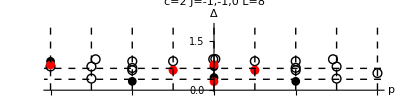

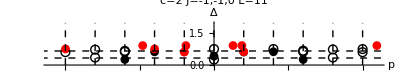

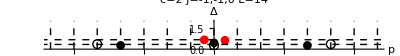

```mathematica
plots = Table[SpectrumIncludingFit[L0,j,q],{L0,8,14,3},{j,{"-1,-1,0"}},{q,0,0}]//Flatten;
Print[#]&/@plots;
```

### Spin-charge relation

```mathematica
SpinCharge2Momentum[k_,L_,s_,q_] := Module[{x = Floor[L/3],y=Mod[L,3],t=3(s-k/9),Q=3q},
(k+Q y)/9+(t+Q x)/3
]
```

```mathematica
Table[SpinCharge2Momentum[0,L,4/3,1],{L,{7,8,10,11,13,14}}]
```

{11/3,4,14/3,5,17/3,6}

```mathematica
Momentum2SpinCharge[k_,L_,p_,tmax_] := Module[{x = Floor[L/3],y=Mod[L,3],t,Q},
{k/9+t/3,Q/9}/.Solve[{p==(k+Q y)/9+(t+Q x)/3,Q∈Integers,t∈Integers,Abs[t]<tmax},{t,Q}]
]
```

```mathematica
Momentum2SpinCharge[0,10,5,8]
```

{{-5/3,2/3},{5/3,1/3}}